```mathematica
CollatzList[n_]:=Module[
{result={}, current =n},
While[current ≠ 1,
AppendTo[result,current];
If[Mod[current,2]==0,
current = Quotient[current,2],
current = current *3 +1
]
];
result
]
```

```mathematica
CollatzList[27]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2}

```mathematica
Map[IntegerDigits[#,6]&, CollatzList[27]]
```

{{4,3},{2,1,4},{1,0,5},{3,2,4},{1,4,2},{5,1},{2,3,4},{1,1,5},{3,5,4},{1,5,5},{5,5,4},{2,5,5},{1,2,5,4},{4,2,5},{2,1,2,4},{1,0,4,2},{3,2,1},{1,4,0,4},{5,0,2},{2,3,1},{1,1,3,4},{3,4,5},{1,5,2,4},{5,4,2},{2,5,1},{1,2,3,4},{4,1,5},{2,0,5,4},{1,0,2,5},{3,1,2,4},{1,3,4,2},{4,5,1},{2,2,3,4},{1,1,1,5},{3,3,5,4},{1,4,5,5},{5,2,5,4},{2,4,2,5},{1,2,1,2,4},{4,0,4,2},{2,0,2,1},{1,0,1,0,4},{3,0,3,2},{1,3,1,4},{4,3,5},{2,1,5,4},{1,0,5,5},{3,2,5,4},{1,4,2,5},{5,1,2,4},{2,3,4,2},{1,1,5,1},{3,5,3,4},{1,5,4,5},{5,5,2,4},{2,5,4,2},{1,2,5,1},{4,2,3,4},{2,1,1,5},{1,0,3,5,4},{3,1,5,5},{1,3,5,5,4},{4,5,5,5},{2,2,5,5,4},{1,1,2,5,5},{3,4,2,5,4},{1,5,1,2,5},{5,3,4,2,4},{2,4,5,1,2},{1,2,2,3,4},{4,1,1,5},{2,0,3,5,4},{1,0,1,5,5},{3,0,5,5,4},{1,3,2,5,5},{4,4,2,5,4},{2,2,1,2,5},{1,1,0,4,2,4},{3,3,2,1,2},{1,4,4,0,4},{5,2,0,2},{2,4,0,1},{1,2,0,0,4},{4,0,0,2},{2,0,0,1},{1,0,0,0,4},{3,0,0,2},{1,3,0,1},{4,3,0,4},{2,1,3,2},{1,0,4,4},{3,2,2},{1,4,1},{5,0,4},{2,3,2},{1,1,4},{3,5},{1,5,4},{5,5},{2,5,4},{1,2,5},{4,2,4},{2,1,2},{1,0,4},{3,2},{1,4},{5},{2,4},{1,2},{4},{2}}

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

ArrayPlot::mat: Argument Transpose[{}] at position 1 is not a list of lists.

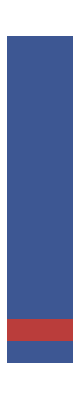
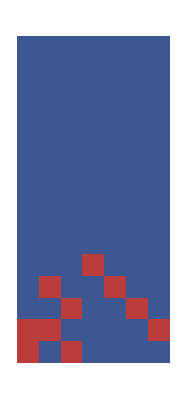
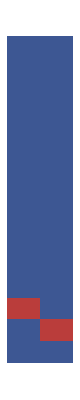
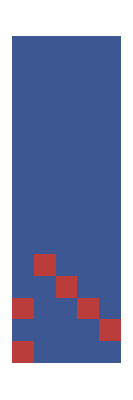
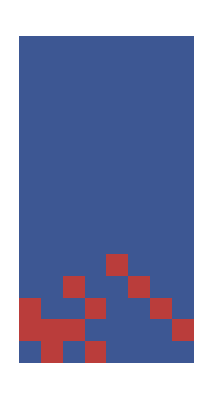
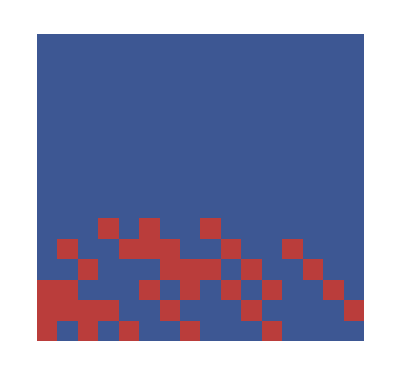
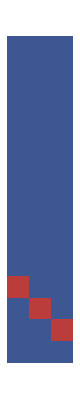
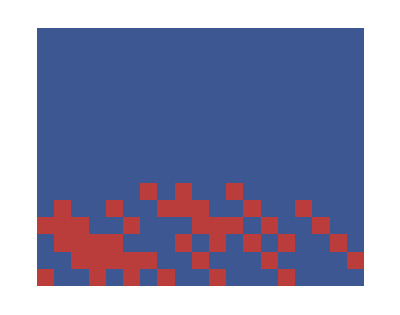
{{1,ArrayPlot[Transpose[{}],ColorFunction→DarkRainbow]},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-},{11,-Graphics-},{12,-Graphics-},{13,-Graphics-},{14,-Graphics-},{15,-Graphics-},{16,-Graphics-},{17,-Graphics-},{18,-Graphics-},{19,-Graphics-},{20,-Graphics-},{21,-Graphics-},{22,-Graphics-},{23,-Graphics-},{24,-Graphics-},{25,-Graphics-},{26,-Graphics-},{27,-Graphics-},{28,-Graphics-},{29,-Graphics-},{30,-Graphics-},{31,-Graphics-},{32,-Graphics-},{33,-Graphics-},{34,-Graphics-},{35,-Graphics-},{36,-Graphics-},{37,-Graphics-},{38,-Graphics-},{39,-Graphics-},{40,-Graphics-},{41,-Graphics-},{42,-Graphics-},{43,-Graphics-},{44,-Graphics-},{45,-Graphics-},{46,-Graphics-},{47,-Graphics-},{48,-Graphics-},{49,-Graphics-},{50,-Graphics-},{51,-Graphics-},{52,-Graphics-},{53,-Graphics-},{54,-Graphics-},{55,-Graphics-},{56,-Graphics-},{57,-Graphics-},{58,-Graphics-},{59,-Graphics-},{60,-Graphics-},{61,-Graphics-},{62,-Graphics-},{63,-Graphics-},{64,-Graphics-},{65,-Graphics-},{66,-Graphics-},{67,-Graphics-},{68,-Graphics-},{69,-Graphics-},{70,-Graphics-},{71,-Graphics-},{72,-Graphics-},{73,-Graphics-},{74,-Graphics-},{75,-Graphics-},{76,-Graphics-},{77,-Graphics-},{78,-Graphics-},{79,-Graphics-},{80,-Graphics-},{81,-Graphics-},{82,-Graphics-},{83,-Graphics-},{84,-Graphics-},{85,-Graphics-},{86,-Graphics-},{87,-Graphics-},{88,-Graphics-},{89,-Graphics-},{90,-Graphics-},{91,-Graphics-},{92,-Graphics-},{93,-Graphics-},{94,-Graphics-},{95,-Graphics-},{96,-Graphics-},{97,-Graphics-},{98,-Graphics-},{99,-Graphics-},{100,-Graphics-}}

```mathematica
Table[{i,ArrayPlot[Transpose[Map[PadLeft[IntegerDigits[#,2],15]&, CollatzList[i]]], ColorFunction->"DarkRainbow"]},{i,1,100}]
```